```mathematica
Get["BSFfast_20251228/BSFfast.m"]
```

```mathematica
?BSFfastSigmavEffBSF
```

(*SM-QCD models: {"QCD-SU","QCD-FU","QCD-SD","QCD-FD","QCD-S","QCD-F"}*)
	(* → αs: {"Cut","Plat"}*)
(*dQCD/dQED models: {"dQCD-S","dQCD-F","dQED-S","dQED-F","dQED-S_nT","dQED-F_nT"}*)
	(* → α some number. (UVi warnings yet to be implemented)*)

```mathematica
BSFfastSigmavEffBSF["QCD-FU","Cut"][10^7.,12345.6]//AbsoluteTiming
```

{0.000027,1.09377×10^-14}

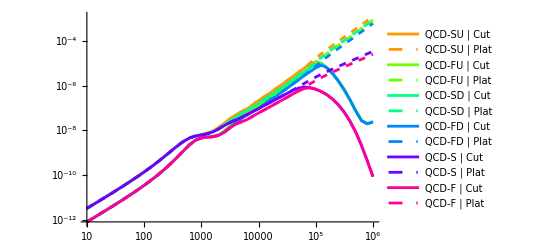

```mathematica
fn=Join@@Table[Legended[BSFfastSigmavEffBSF[model,as][10^4.,x],model<>" | "<>as],{model,{"QCD-SU","QCD-FU","QCD-SD","QCD-FD","QCD-S","QCD-F"}},{as,{"Cut","Plat"}}]//Evaluate;
LogLogPlot[fn,{x,10,10^6},PlotStyle->Flatten[{{Bold,#},{Dashed,#}}&/@Hue/@Range[.1,.9,.8/5],1]]
```

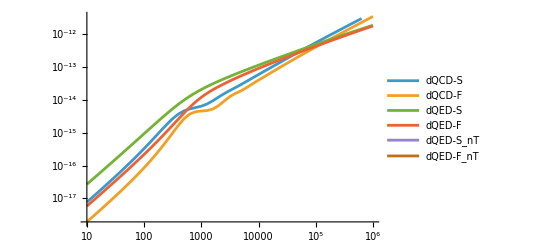

```mathematica
fnresc=Table[Legended[BSFfastSigmavEffBSF[model,0.1][10^7.,x],model],{model,{"dQCD-S","dQCD-F","dQED-S","dQED-F","dQED-S_nT","dQED-F_nT"}}]//Evaluate;
LogLogPlot[fnresc,{x,10,10^6}]
```